```mathematica
Quit[]
```

```mathematica
<<pkg`
```

```mathematica
m1=1.5;m2=1; λi=0;λf=2; (*G=1;*) (*ϵ*)


Rinit={1,.5,1.5};
Pinit=(*p*)(.1) *{1,-4,-1};  (*-0.23177026220258928<p<0.23233759931552855 will make energy negative*)
S1init={1,1,1.9};
S2init={0,0,1}-Cross[Rinit,Pinit]-S1init;
```

```mathematica
SeffLflow[m1,m2,Rinit,Pinit,S1init,S2init,λf,λi]
NmSeffLflow[m1,m2,Rinit,Pinit,S1init,S2init,λf,λi]
```

{{1.43898,-0.269555,-1.16476},{-0.026334,-0.334587,0.259534},{-0.418048,-1.47254,1.80745},{0.877722,1.81533,-0.318886}}

{{1.43898,-0.269555,-1.16476},{-0.026334,-0.334587,0.259534},{-0.418048,-1.47254,1.80745},{0.877722,1.81533,-0.318885}}

```mathematica
Jsqflow[m1,m2,Rinit,Pinit,S1init,S2init,λf,λi]
NmJsqflow[m1,m2,Rinit,Pinit,S1init,S2init,λf,λi]
Lsqflow[m1,m2,Rinit,Pinit,S1init,S2init,λf,λi]
 NmLsqflow[m1,m2,Rinit,Pinit,S1init,S2init,λf,λi]
Jzflow[m1,m2,Rinit,Pinit,S1init,S2init,λf,λi]
NmJzflow[m1,m2,Rinit,Pinit,S1init,S2init,λf,λi]
```

{{-0.275242,-1.08362,1.5},{-0.368085,0.185777,-0.1},{0.103159,-1.41045,1.9},{0.0671445,1.9901,-0.45}}

{{-0.275242,-1.08362,1.5},{-0.368085,0.185777,-0.1},{0.103159,-1.41045,1.9},{0.0671441,1.9901,-0.45}}

{{-0.889884,-0.712424,-1.48343},{-0.133993,0.398411,0.0575699},{1.,1.,1.9},{-1.55,-1.25,-0.45}}

{{-0.889884,-0.712425,-1.48343},{-0.133993,0.398411,0.0575697},{1.,1.,1.9},{-1.55,-1.25,-0.45}}

{{-0.870796,0.701224,1.5},{0.322104,0.257388,-0.1},{-1.32544,0.493151,1.9},{1.78165,-0.889227,-0.45}}

{{-0.870795,0.701224,1.5},{0.322104,0.257388,-0.1},{-1.32544,0.493151,1.9},{1.78165,-0.889227,-0.45}}

The energy for the initial data is

-0.653733

The frequencies are

{-0.022846,0.,1.39177,1.27137,-0.00308126}

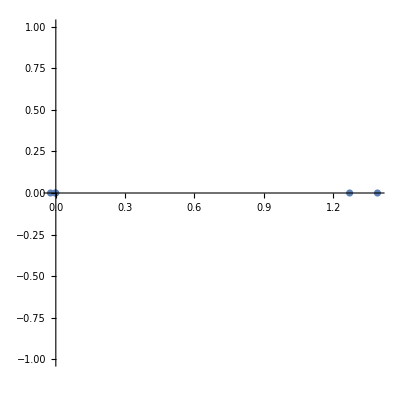

```mathematica
frequency[m1,m2,Rinit,Pinit,S1init,S2init,λf,λi]
```

```mathematica
(*
(*data needed to check if the energy is negative*)
ϵ= 3/1000; spinSuppressFac = ϵ^(1/2);    c = 1/spinSuppressFac   ;
 μ =m1  m2 /(m1+m2); M=m1+m2;
Q1=(2+3 m2/(2 m1));Q2=(2+3 m1/(2 m2));
Linit=Cross[Rinit, Pinit];
SeffLN=(Q1 S1init+ Q2 S2init).Linit;
En=μ ((Pinit.Pinit)/(2 μ^2)-(G M)/Norm[Rinit]) + (G ϵ SeffLN)/(Norm[Rinit])^3 //Simplify*)
```